## Introduction

Can we analyze the sync state using the technique in “Collective dynamics of coupled oscillators with random pinning” section 2.1?

## Look at state

### Scatter plots

```mathematica
(*Preamble*)
{dt,n,T}={0.25,100,500}; 
{J,k}={1,2};
{e,b}={0,0.25};

{Ex,Eθ} = {e,e};
{b1,b2} = {b,b}

{z0,pin,znew}={Table[RandomReal[{1.99π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

results={};
Dynamic[results] (*For dynamic plotting*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
results=plotResults[znew,pin]
]
```

{0.25,0.25}

$Aborted

### S(b) for K = 2

```mathematica
data1=ParallelTable[
{dt,n,T}={0.5,200,100}; 
{J,k}={1,2};
{Ex,Eθ} = {0,0};
b=b1;
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{b1,Sp,Sm},
{b1,-1.5,1.5,0.025}
];
```

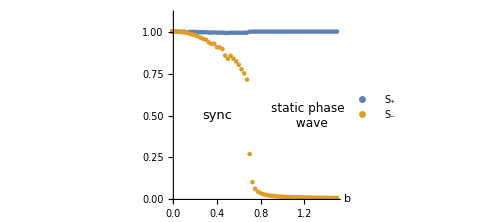

```mathematica
p1=ListPlot[{data1[[All,{1,2}]],data1[[All,{1,3}]]},AxesLabel->{Style["b",25,Italic]},PlotLegends->{Style["S_+",17,Italic],Style["S_-",17,Italic]},AxesStyle->15,Epilog->{Text[Style["K = 2",16,Italic],{-1.25,0.8}],Text[Style["static phase \n wave",12],{1.25,0.5}],Text[Style["sync",13],{0.4,0.5}]},ImageSize->Medium,PlotRange->{{0,1.5},{0,1.1}}]
```

1. So it looks like S_+=1 for all b. Use this.

## Fixed points: via exponentials

Goal: parameterize the fixed points in terms of exponentials

```mathematica
e1=b/(2 ⅈ)(ⅇ^(ⅈ(x-α))-ⅇ^(-ⅈ(x-α)))+1/(4ⅈ)sp(ⅇ^(ⅈ(ϕp-x+θ))-ⅇ^(-ⅈ(ϕp-x+θ)))+1/(4ⅈ)sm(ⅇ^(ⅈ(ϕm-x-θ))-ⅇ^(-ⅈ(ϕp-x-θ)));
e2=b/(2 ⅈ)(ⅇ^(ⅈ(θ-α))-ⅇ^(-ⅈ(θ-α)))+k/(4 ⅈ)sp(ⅇ^(ⅈ(ϕp-x+θ))-ⅇ^(-ⅈ(ϕp-x+θ)))-k/(4 ⅈ)sm(ⅇ^(ⅈ(ϕm-x-θ))-ⅇ^(-ⅈ(ϕp-x-θ)));
es={e1,e2};
es1=simplifyExponents[Simplify[es*ⅇ^(ⅈ x)*ⅇ^(ⅈ θ)]];
es1=es1/.{ⅇ^(2 ⅈ x)->z^2,ⅇ^(2 ⅈ θ)->w^2,ⅇ^(2 ⅈ (x+θ))->z^2 w^2,ⅇ^(2 ⅈ (θ+ϕp))->w^2 ⅇ^(2 ⅈ ϕp),ⅇ^(ⅈ (x+ϕp))->z ⅇ^(ⅈ ϕp),ⅇ^(ⅈ (θ+ϕp))->w ⅇ^(ⅈ ϕp) };
es2={es1[[1]][[3]],es1[[2]][[3]]};
es2=Collect[es2,{w,z,w z,w z^2}];
TableForm[es2]
```

-ⅇ^(ⅈ α+ⅈ (ϕm+ϕp)) sm+ⅇ^(ⅈ α) sp z^2+w (2 b ⅇ^(2 ⅈ α+ⅈ ϕp)-2 b ⅇ^(ⅈ ϕp) z^2)+w^2 (-ⅇ^(ⅈ α+2 ⅈ ϕp) sp+ⅇ^(ⅈ α) sm z^2)
ⅇ^(ⅈ α+ⅈ (ϕm+ϕp)) k sm+2 b ⅇ^(2 ⅈ α+ⅈ ϕp) z+ⅇ^(ⅈ α) k sp z^2+w^2 (-ⅇ^(ⅈ α+2 ⅈ ϕp) k sp-2 b ⅇ^(ⅈ ϕp) z-ⅇ^(ⅈ α) k sm z^2)

#### Warm up: b = 0

```mathematica
es3=es2/.b->0/.α->0
```

{-ⅇ^(ⅈ (ϕm+ϕp)) sm+sp z^2+w^2 (-ⅇ^(2 ⅈ ϕp) sp+sm z^2),ⅇ^(ⅈ (ϕm+ϕp)) k sm+k sp z^2+w^2 (-ⅇ^(2 ⅈ ϕp) k sp-k sm z^2)}

```mathematica
Solve[es3=={0,0},{w,z}]//Simplify//TableForm
```

w→-ⅇ^(1/4 ⅈ (ϕm-ϕp)) | z→-ⅇ^(1/4 ⅈ (ϕm+3 ϕp))
w→ⅇ^(1/4 ⅈ (ϕm-ϕp)) | z→-ⅇ^(1/4 ⅈ (ϕm+3 ϕp))
w→-ⅈ ⅇ^(1/4 ⅈ (ϕm-ϕp)) | z→-ⅈ ⅇ^(1/4 ⅈ (ϕm+3 ϕp))
w→ⅈ ⅇ^(1/4 ⅈ (ϕm-ϕp)) | z→-ⅈ ⅇ^(1/4 ⅈ (ϕm+3 ϕp))
w→-ⅈ ⅇ^(1/4 ⅈ (ϕm-ϕp)) | z→ⅈ ⅇ^(1/4 ⅈ (ϕm+3 ϕp))
w→ⅈ ⅇ^(1/4 ⅈ (ϕm-ϕp)) | z→ⅈ ⅇ^(1/4 ⅈ (ϕm+3 ϕp))
w→-ⅇ^(1/4 ⅈ (ϕm-ϕp)) | z→ⅇ^(1/4 ⅈ (ϕm+3 ϕp))
w→ⅇ^(1/4 ⅈ (ϕm-ϕp)) | z→ⅇ^(1/4 ⅈ (ϕm+3 ϕp))

```mathematica
es2[[2]]/.{sp->SubPlus[S],sm->SubMinus[S],ϕp->SubPlus[ϕ],ϕm->SubMinus[ϕ],k->K}//TeXForm
```

w^2 \left(-2 b z e^{i \phi _+}-K S_+ e^{i \alpha +2 i \phi _+}-e^{i \alpha } K S_- z^2\right)+2 b z e^{2 i \alpha +i \phi _+}+K S_- e^{i \alpha +i \left(\phi _-+\phi _+\right)}+e^{i \alpha } K S_+
   z^2

#### Warm up: ϕ+=ϕ-=0

```mathematica
es3=es2/.{ϕp->0,ϕm->0};
fp=Solve[es3=={0,0},{w,z}]
```

{{w→Root[-b^2 ⅇ^(5 ⅈ α) sm sp+ⅇ^(3 ⅈ α) k^2 sm^2 sp^2+(2 b^3 ⅇ^(4 ⅈ α) sm+2 b^3 ⅇ^(6 ⅈ α) sp-2 b ⅇ^(2 ⅈ α) k^2 sm^2 sp-2 b ⅇ^(4 ⅈ α) k^2 sm sp^2) #1+(-4 b^4 ⅇ^(5 ⅈ α)-b^2 ⅇ^(5 ⅈ α) sm^2+b^2 ⅇ^(ⅈ α) k^2 sm^2+2 b^2 ⅇ^(3 ⅈ α) sm sp+2 b^2 ⅇ^(3 ⅈ α) k^2 sm sp-b^2 ⅇ^(5 ⅈ α) sp^2+b^2 ⅇ^(5 ⅈ α) k^2 sp^2) #1^2+(-4 b^3 ⅇ^(2 ⅈ α) sm+2 b^3 ⅇ^(6 ⅈ α) sm-2 b^3 ⅇ^1 sp+2 b ⅇ^1 k^2 sm^2 sp+2 b ⅇ^(2 ⅈ α) k^2 sm sp^2) #1^3+(1)11+(2 b^3 sm-4 b^3 ⅇ^(4 ⅈ α) sm-2 b^3 ⅇ^(2 ⅈ α) sp+2 b ⅇ^(2 ⅈ α) k^2 sm^2 sp+2 b ⅇ^(4 ⅈ α) k^2 sm sp^2) #1^5+(-4 b^4 ⅇ^(ⅈ α)-b^2 ⅇ^(ⅈ α) sm^2+b^2 ⅇ^(5 ⅈ α) k^2 sm^2+2 b^2 ⅇ^(3 ⅈ α) sm sp+2 b^2 ⅇ^(3 ⅈ α) k^2 sm sp-b^2 ⅇ^(ⅈ α) sp^2+b^2 ⅇ^(ⅈ α) k^2 sp^2) #1^6+(2 b^3 ⅇ^(2 ⅈ α) sm+2 b^3 sp-2 b ⅇ^(4 ⅈ α) k^2 sm^2 sp-2 b ⅇ^(2 ⅈ α) k^2 sm sp^2) #1^7+(-b^2 ⅇ^(ⅈ α) sm sp+ⅇ^(3 ⅈ α) k^2 sm^2 sp^2) #1^8&,1],z→1},6,1}
 |  |  |  |

```mathematica
Length[fp]
```

8

```mathematica
fp1=fp/.b->0.25/.α->0.1/.k->2/.sp->1/.sm->0.5
```

{{w→-0.999939+0.0110728 ⅈ,z→-0.999753-0.0222134 ⅈ},{w→-0.999734-0.0230689 ⅈ,z→0.999527+0.0307556 ⅈ},{w→0.30958-0.950873 ⅈ,z→-0.0629417-0.998017 ⅈ},{w→0.317903+0.948123 ⅈ,z→-0.0486213+0.998817 ⅈ},{w→0.417748+0.908563 ⅈ,z→-0.304184-0.952613 ⅈ},{w→0.448191-0.893938 ⅈ,z→-0.331829+0.943339 ⅈ},{w→0.998756-0.0498575 ⅈ,z→-0.997214+0.0745898 ⅈ},{w→1.+0.00006206 ⅈ,z→0.998764-0.0496999 ⅈ}}

```mathematica
fp1//TableForm
```

w→-0.999939+0.0110728 ⅈ | z→-0.999753-0.0222134 ⅈ
w→-0.999734-0.0230689 ⅈ | z→0.999527+0.0307556 ⅈ
w→0.30958-0.950873 ⅈ | z→-0.0629417-0.998017 ⅈ
w→0.317903+0.948123 ⅈ | z→-0.0486213+0.998817 ⅈ
w→0.417748+0.908563 ⅈ | z→-0.304184-0.952613 ⅈ
w→0.448191-0.893938 ⅈ | z→-0.331829+0.943339 ⅈ
w→0.998756-0.0498575 ⅈ | z→-0.997214+0.0745898 ⅈ
w→1.+0.00006206 ⅈ | z→0.998764-0.0496999 ⅈ

## Fixed points: non exponentials

### Simplification: assume ϕ_+=ϕ_-=b=0

Recover the sync state when b = 0

```mathematica
vx=-b Sin[x-α]+sp j/2 Sin[ϕp-(x+θ)]+sm j/2 Sin[ϕm-(x-θ)];
vtheta=-b Sin[θ-α]+sp k/2 Sin[ϕp-(x+θ)]-sm j/2 Sin[ϕm-(x-θ)];
subs={j->1,b->0,ϕp->0,ϕm->0};
es={vx,vtheta}/.subs;
fp=Solve[es=={0,0},{x,θ}];
TableForm[fp]
```

x→ConditionalExpression[2 π C[1], C[1]∈ℤ] | θ→ConditionalExpression[-2 π C[2], C[2]∈ℤ]
x→ConditionalExpression[2 π C[1], C[1]∈ℤ] | θ→ConditionalExpression[-π-2 π C[2], C[2]∈ℤ]
x→ConditionalExpression[-π/2+2 π C[1], C[1]∈ℤ] | θ→ConditionalExpression[-π/2-2 π C[2], C[2]∈ℤ]
x→ConditionalExpression[-π/2+2 π C[1], C[1]∈ℤ] | θ→ConditionalExpression[π/2-2 π C[2], C[2]∈ℤ]
x→ConditionalExpression[π/2+2 π C[1], C[1]∈ℤ] | θ→ConditionalExpression[-π/2-2 π C[2], C[2]∈ℤ]
x→ConditionalExpression[π/2+2 π C[1], C[1]∈ℤ] | θ→ConditionalExpression[π/2-2 π C[2], C[2]∈ℤ]
x→ConditionalExpression[π+2 π C[1], C[1]∈ℤ] | θ→ConditionalExpression[-2 π C[2], C[2]∈ℤ]
x→ConditionalExpression[π+2 π C[1], C[1]∈ℤ] | θ→ConditionalExpression[-π-2 π C[2], C[2]∈ℤ]

Good. Now turn b back on

```mathematica
vx=-b Sin[x-α]+sp j/2 Sin[ϕp-(x+θ)]+sm j/2 Sin[ϕm-(x-θ)];
vtheta=-b Sin[θ-α]+sp k/2 Sin[ϕp-(x+θ)]-sm j/2 Sin[ϕm-(x-θ)];
subs={j->1,ϕp->0,ϕm->0,sp->1};
es={vx,vtheta}/.subs;
fp=Solve[es=={0,0},{x,θ}];
TableForm[fp]
```

$Aborted

x→ConditionalExpression[2 π C[1], C[1]∈ℤ] | θ→ConditionalExpression[-2 π C[2], C[2]∈ℤ]
x→ConditionalExpression[2 π C[1], C[1]∈ℤ] | θ→ConditionalExpression[-π-2 π C[2], C[2]∈ℤ]
x→ConditionalExpression[-π/2+2 π C[1], C[1]∈ℤ] | θ→ConditionalExpression[-π/2-2 π C[2], C[2]∈ℤ]
x→ConditionalExpression[-π/2+2 π C[1], C[1]∈ℤ] | θ→ConditionalExpression[π/2-2 π C[2], C[2]∈ℤ]
x→ConditionalExpression[π/2+2 π C[1], C[1]∈ℤ] | θ→ConditionalExpression[-π/2-2 π C[2], C[2]∈ℤ]
x→ConditionalExpression[π/2+2 π C[1], C[1]∈ℤ] | θ→ConditionalExpression[π/2-2 π C[2], C[2]∈ℤ]
x→ConditionalExpression[π+2 π C[1], C[1]∈ℤ] | θ→ConditionalExpression[-2 π C[2], C[2]∈ℤ]
x→ConditionalExpression[π+2 π C[1], C[1]∈ℤ] | θ→ConditionalExpression[-π-2 π C[2], C[2]∈ℤ]

## Plot vector field and null clines

1. Here I want to see where the fixed points and nullclines lie, visually. 
2. I’m hoping some tangency condition or something will spill out

```mathematica
vx=-b Sin[x-α]+sp j/2 Sin[ϕp-(x+θ)]+sm j/2 Sin[ϕm-(x-θ)];
vtheta=-b Sin[θ-α]+sp k/2 Sin[ϕp-(x+θ)]-sm j/2 Sin[ϕm-(x-θ)];

Manipulate[
p1=VectorPlot[{vx,vtheta}/.{b->b1,j->1,k->k1,sp->sp1,sm->sm1,α->α1,ϕp->0,ϕm->ϕ1},{x,-π,π},{θ,-π,π},VectorColorFunction->Black];
p2=ContourPlot[{
(vx/.{b->b1,j->1,k->k1,sp->sp1,sm->sm1,α->α1,ϕp->0,ϕm->ϕ1})==0,
(vtheta/.{b->b1,j->1,k->k1,sp->sp1,sm->sm1,α->α1,ϕp->0,ϕm->ϕ1})==0
},{x,-π,π},{θ,-π,π}];
Show[{p1,p2}]
,
{{b1,0.5},0,2},{{k1,2},-3,3},{{sp1,0.9},0,1},{{sm1,0.8},0,1},{{α1,0.1},0,2π},{{ϕ1,π/3},0,2π}
]
```

Hmm, I see what’s happening, but its still hard to pull anything out analytically.

## Functions

```mathematica
rhs=Compile[{{z,_Real,2},{n,_Integer},{J,_Real},{k,_Real}, {Ex,_Real}, {Eθ, _Real}, {pin, _Real, 2}, {b1,_Real},{b2,_Real}},
Module[{i,j,xji,yji,thetaji,inverseDistSq,inverseDist,xtemp,ytemp,thetatemp,rep,A,B,C,n1,vel=ConstantArray[0.0,{2,n}]},
{A,B,C,n1}={1,1,10,1};
For[i=1,i≤n,i++,
vel[[1,i]] = Ex + b1*Sin[pin[[1,i]] - z[[1,i]]];
vel[[2,i]] = Eθ + b2*Sin[pin[[2,i]] - z[[2,i]]];
];
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
xji=z[[1,j]]-z[[1,i]];
thetaji=z[[2,j]]-z[[2,i]];
xtemp=J*Sin[xji]*Cos[thetaji]/N[n];
thetatemp=k*Sin[thetaji]*Cos[xji]/N[n];
vel[[1,i]]+=xtemp;vel[[1,j]]+=-xtemp;
vel[[2,i]]+=thetatemp;vel[[2,j]]+=-thetatemp;
];
];
vel
(*vel/N[n]*)
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];

findWs[z_]:=Block[{Wp,Wm,i,numOsc},
{Wp,Wm}={0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Wp+=Exp[ⅈ (z[[1,i]]+z[[2,i]])];
Wm+=Exp[ⅈ (z[[1,i]]-z[[2,i]])];
];
Return[{Wp/numOsc,Wm/numOsc}]
]

plotResults[z_,pin_]:=Block[{colors,Wp,Wm,p1,p2,p3,p4,p5,x,θ,xin,θin},
{x,θ}={z[[1,All]],z[[2,All]]};
{xin,θin}={pin[[1,All]],pin[[2,All]]};
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[θ,2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];

p1=Graphics[{
(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],

Cyan,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Magenta,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],

Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];


(*Scatter plot in (x,theta) space*)
p2=ListPlot[{x//mod,θ//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}];

(*Scatter plot in (ξ,θ) space*)
p3=ListPlot[{x+θ,x-θ}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]}];

p4=ListPlot[{x,xin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["β",15]}];

p5=ListPlot[{θ,θin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["θ",15],Style["α",15]}];

Return[Grid[{{p1,p2,p3,p4,p5}}]
]
];


eulerStep[z_,F_,dt_,J_,k_,Ex_,Eθ_,pin_,b1_,b2_]:=Block[{znew,n,i,j,vel},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
vel=F[z,n,J,k,Ex,Eθ,pin,b1,b2];
znew=z+dt*vel;
Return[znew]
];

rk4[z_,F_,dt_,J_,k_,Ex_,Eθ_,pin_,b1_,b2_]:=Block[{znew,n,i,j,k1,k2,k3,k4},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
k1=F[z,n,J,k,Ex,Eθ,pin,b1,b2];
k2=F[z+dt/2 k1,n,J,k,Ex,Eθ,pin,b1,b2];
k3=F[z+dt/2 k2,n,J,k,Ex,Eθ,pin,b1,b2];
k4=F[z+dt k3,n,J,k,Ex,Eθ,pin,b1,b2];
Return[z+dt/6(k1+2k2+2k3+k4)]
];

mod[θ_]:=Return[Mod[θ,2π]-π];

findMeanV[znew_,z_,dt_]:=Block[{v},
v=(znew-z)/dt;
v=(v[[1,All]]^2+v[[2,All]]^2)^(1/2);
Return[Mean[v]]
];

findGamma[xs_,θs_,cutoff_]:=Block[{gammas,i,n,x,θ,xSteady,rangeSteadyX,gammaX,θSteady,rangeSteadyθ,gammaθ,index},
(*Find fraction of swarmalators that have completed at least 
 one full oscillation (0,2π) mod 2π, after transients have been discarded *)

n= Dimensions[xs][[2]];
gammas={};
For[i=1,i≤n,i++,
{x,θ}={xs[[All,i]],θs[[All,i]]};

(*Check for one loop when x has approximately achieved its steady state*)
xSteady=x[[cutoff;;-1]];
rangeSteadyX=Max[xSteady]-Min[xSteady];
gammaX=If[rangeSteadyX>=2π,1,0];

(*Check for one loop when θ has approximately achieved its steady state*)
θSteady=θ[[cutoff;;-1]];
rangeSteadyθ=Max[θSteady]-Min[θSteady];
gammaθ=If[rangeSteadyθ>=2π,1,0];

(*Require both to be true*)
AppendTo[gammas,gammaX*gammaθ]
];

(*Return fraction of swarmalators with gamma = 1*)
Return[Mean[gammas]]
];

plotResults[z_,pin_]:=Block[{colors,Wp,Wm,p1,p2,p3,p4,p5,x,θ,xin,θin,x1,θ1,x2,θ2,ξ1,ξ2,η1,η2,index,n},
{x,θ}={z[[1,All]],z[[2,All]]};
{xin,θin}={pin[[1,All]],pin[[2,All]]};
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[θ,2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];

p1=Graphics[{
(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],

Cyan,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Magenta,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],

Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];


(*Scatter plot in (x,theta) space*)
n=Length[x];
index=Round[n/2];
{x1,θ1}={x[[1]],θ[[1]]};
{x2,θ2}={x[[index]],θ[[index]]};
p2=ListPlot[{x//mod,θ//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]},Epilog->{Cyan,PointSize[0.025],Point[{x1,θ1}//mod],Magenta,Point[{x2,θ2}//mod]}];

(*Scatter plot in (ξ,θ) space*)
{ξ1,η1}={x[[1]]+θ[[1]],x[[1]]-θ[[1]]};
{ξ2,η2}={x[[index]]+θ[[index]],x[[index]]-θ[[index]]};
p3=ListPlot[{x+θ,x-θ}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]},Epilog->{Cyan,PointSize[0.025],Point[{ξ1,η1}//mod],Magenta,Point[{ξ2,η2}//mod]}];

p4=ListPlot[{x,xin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["β",15]}];

p5=ListPlot[{θ,θin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["θ",15],Style["α",15]}];

Return[Grid[{{p1,p2,p3,p4,p5}}]
]
];

simplifyExponents[eqn_]:=Block[{},
Return[eqn/. {Exp[x_]:>Exp[Together@FullSimplify[x]]}]]
eqn=simplifyExponents[eqn];
```